```mathematica
img=Import["E:\\MISC\\Image\\99fb3cad6e3566c962ab10c969ae6720.jpg"]
```

-Graphics-

```mathematica
EdgeDetect[Blur[img,3]]
```

-Graphics-

```mathematica
Binarize[EdgeDetect[Blur[img,3]]]
```

-Graphics-

```mathematica
el=ImageMeasurements[Binarize[EdgeDetect[Blur[img,3]]],"Contours"]
```

{Line[{{276,366},{276,365},{276,365},{212,365},{212,364},{212,364},213,{282,365},{278,365},{278,365},{278,366},{276,366}}],239,1}
 |  |  |  |

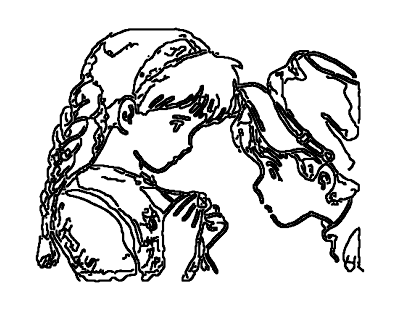

```mathematica
Graphics[el]
```

```mathematica
Rasterize@Graphics[el]
```

-Graphics-

```mathematica
ImageMeasurements[Rasterize@Graphics[el],"Contours"]
```

{Line[{{0,282},{0,0},{360,0},{360,282},{0,282}}],445,Line[{{118,10},{118,10},{119,10},{119,10},{119,9},{119,9},{118,9},{118,9},{118,10}}]}
 |  |  |  |

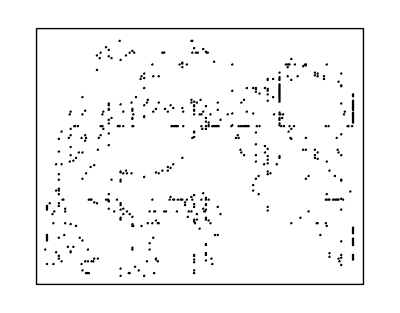

```mathematica
Graphics@%51
```

```mathematica
Length[Line[{1,2,1,6,5,5}][[1]]]
```

6

```mathematica
Line[{1,2,1,6,5,5}][[0]]
```

Line

```mathematica
Fourier
```

```mathematica
img=Import["https://i.stack.imgur.com/wtJoA.png"]
```

-Graphics-

```mathematica
Binarize[img~ColorConvert~"Grayscale"~ImageResize~500~Blur~3]
```

-Graphics-

```mathematica
Binarize[img]
```

-Graphics-